```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
rho=Flatten[Import["./kappa.dat"]];
lam1=Flatten[Import["./lam1.dat"]];
lam2=Flatten[Import["./lam2.dat"]];
k=Flatten[Import["./k1.dat"]];
rhobar=rho/k;
```

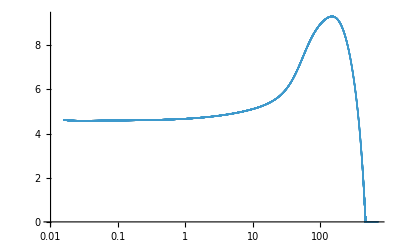

```mathematica
ListPlot[Transpose[{k,rhobar}],PlotRange->All,ScalingFunctions->{"Log",Automatic}]
```

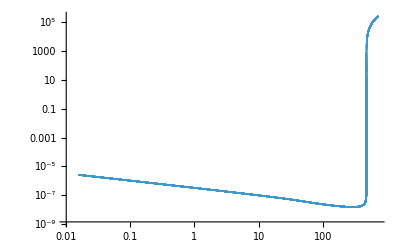

```mathematica
ListPlot[Transpose[{k,lam1}],PlotRange->{All,All},ScalingFunctions->{"Log","Log"}]
```

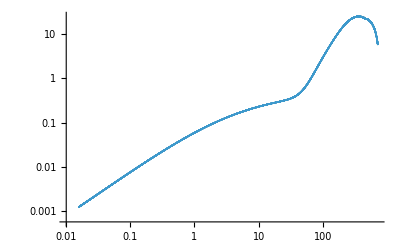

```mathematica
ListPlot[Transpose[{k,lam2}],PlotRange->All,ScalingFunctions->{"Log","Log"}]
```